# Baryon Code Tests

## Gubser Tests

## Setup

### working directory

```mathematica
wd=SetDirectory@NotebookDirectory[]
root=ParentDirectory[ParentDirectory[wd]]
```

/Users/Lipei/Documents/GitHub/BEShydro/tests/Plotting

/Users/Lipei/Documents/GitHub/BEShydro

### constants

```mathematica
hbarc=0.197326938;
```

```mathematica
Nc=3;
Nf=2.5;
fac=3(2(Nc^2-1)+7/2Nc*Nf)Pi^2/90;
facT=fac^(1/4);
T0=1.2;
ed[T_]:=fac*T^4;
```

### plot styles

```mathematica
styles={Directive[RGBColor[0,0,0],AbsoluteThickness[4]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0.5],AbsoluteThickness[3],AbsoluteDashing[{10,5}]],Directive[RGBColor[0,0.5,0],AbsoluteThickness[3],AbsoluteDashing[{10,5,2,5}]],Directive[RGBColor[1,0.5,0.0],AbsoluteThickness[3],AbsoluteDashing[{1,4}]],Directive[RGBColor[0.5,0.5,0.5],AbsoluteThickness[2],AbsoluteDashing[{1,4}]]};
```

```mathematica
FrameTicksFontSize=30;
FrameFontSize=30;PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[AbsoluteThickness[1.1]],Directive[AbsoluteThickness[1.1]]},BaseStyle->{FontFamily->"Times",FontSize->30},AspectRatio->0.75,ImageSize->600,PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];
```

### data reader

```mathematica
Off[Interpolation::inhr];
varInt[t_,dir_,var_]:=Interpolation[Import[dir<>"/"<>var<>"_"<>ToString[PaddedForm[t,{4,3},NumberPadding->{"","0"}]]<>".dat"],InterpolationOrder->3]
```

## Ideal Gubser with Baryon

```mathematica
tlist={1.5,2,3};
clist={Red,Blue,Darker[Green]};
```

### analytical solution

```mathematica
e0=ed[T0]
n0=30
```

28.8224

30

```mathematica
utd[t_,x_,y_,{q_}]:=Cosh[ArcTanh[2q t q Sqrt[x^2+y^2]/(1+q^2t^2+q^2(x^2+y^2))]]
uxd[t_,x_,y_,{q_}]:=x*Sinh[ArcTanh[2q t q Sqrt[x^2+y^2]/(1+q^2t^2+q^2(x^2+y^2))]]/Sqrt[x^2+y^2]
ed[t_,x_,y_,{q_}]:=e0*(2q*t)^(8/3)/(t^4(1+2q^2(t^2+x^2+y^2)+q^4(t^2-x^2-y^2)^2)^(3.5/3))
rhod[t_,x_,y_,{q_}]:=n0*(2q*t)^2/(t^3(1+2q^2(t^2+x^2+y^2)+q^4(t^2-x^2-y^2)^2))
```

### load numerical data

```mathematica
outputDir="/Users/Lipei/Documents/GitHub/cpu-vhb/output";
lim=-Import[outputDir<>"/e_"<>ToString[PaddedForm[tlist[[1]],{3,3},NumberPadding->{"","0"}]]<>".dat"][[1,1]];
Clear[eInt,rhobInt,uxInt,utInt]
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt,rhobInt,uxInt,utInt},{"e","rhob","ux","ut"}}];
```

### make plots

```mathematica
edPlot=Show[Table[Plot[{ed[tlist[[i]],x,0,{1}],eInt[i-1][x,0,0]},{x,-5,5},PlotStyle->{{AbsoluteThickness[3],clist[[i]],Opacity[0.5]},{AbsoluteThickness[2],clist[[i]],Dashed}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","ϵ[fm^-4]"},ImageSize->600]
rhodPlot=Show[Table[Plot[{rhod[tlist[[i]],x,0,{1}],rhobInt[i-1][x,0,0]},{x,-5,5},PlotStyle->{{AbsoluteThickness[3],clist[[i]],Opacity[0.5]},{AbsoluteThickness[2],clist[[i]],Dashed}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","N[fm^-3]"},ImageSize->600]
uxPlot=Show[Table[Plot[{uxd[tlist[[i]],x,0,{1}],uxInt[i-1][x,0,0]},{x,-5,5},PlotStyle->{{AbsoluteThickness[3],clist[[i]],Opacity[0.5]},{AbsoluteThickness[2],clist[[i]],Dashed}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","u^x"},ImageSize->600,Epilog->Inset["τ_0="<>ToString[1]<>"fm, T_0=1.2 fm^-1",{-1.5,3},BaseStyle->{FontFamily->"Times",FontSize->20}]]
utPlot=Show[Table[Plot[{utd[tlist[[i]],x,0,{1}],utInt[i-1][x,0,0]},{x,-5,5},PlotStyle->{{AbsoluteThickness[3],clist[[i]],Opacity[0.5]},{AbsoluteThickness[2],clist[[i]],Dashed}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","u^t"},ImageSize->600]
```

```mathematica
Export["gubser_ideal_e.pdf",edPlot]
Export["gubser_ideal_rhob.pdf",rhodPlot]
Export["gubser_ideal_ux.pdf",uxPlot]
Export["gubser_ideal_ut.pdf",utPlot]
```

### numerical issues

central difference theta=1.0

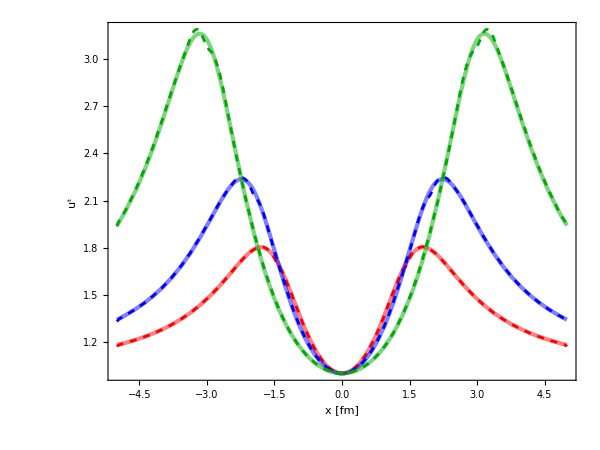

## Conformal Isreal-Stewart Gubser with Baryon

### setup

```mathematica
tlist={1.0,1.5,2.0};
clist={Red,Darker[Green],Blue};
```

### equation of state

```mathematica
hbarc=0.197326938;
Nc=3;
Nf=2.5;
fac=3(2(Nc^2-1)+7/2Nc*Nf)Pi^2/90;
Tint[e_]=(e/fac)^(1/4);
P[e_]=e/3;
```

### transport coefficients

```mathematica
etabar=0.2;
taupiInv[e_]=Tint[e]/(5*etabar);
deltapipi=4/3;
taupipi=0;(*10/7;*)
betapi[e_]=4e/15;
Cb=4;
taunInv[e_]=Tint[e]/Cb;
deltann=1;
lambdann=3/5;
```

### equation of state

```mathematica
T0=1.2;
e0=fac*T0^4;
n0=50;
nn0=20;
```

### equations of motion

```mathematica
Clear[e,pinn,n,nn];
```

```mathematica
{esol,pinnsol,nsol,nnsol}={e,pinn,n,nn}/.NDSolve[{e'[p]==-2e[p]*Tanh[p]-2*e[p]/3*Tanh[p]+pinn[p]*Tanh[p],pinn'[p]+taupiInv[e[p]]*pinn[p]==Tanh[p](4/3*betapi[e[p]]-2*deltapipi*pinn[p]+1/3*taupipi*pinn[p]),
n'[p]+2Tanh[p]n[p]==0,
nn'[p]+taunInv[e[p]]*nn[p]==-Tanh[p]*(2*deltann-2/3*lambdann)*nn[p],e[0]==e0,pinn[0]==0,n[0]==n0,nn[0]==nn0},{e,pinn,n,nn},{p,-10,10}][[1]];
```

### analytical solutions

```mathematica
nm[t_,r_]:=nsol[ArcSinh[-(1-t^2+r^2)/2/t]]/t^3;
nnm[t_,r_]:=nnsol[ArcSinh[-(1-t^2+r^2)/2/t]]/t^4;
urm[t_,r_,{q_}]:=Sinh[ArcTanh[2*q*t*q*Sqrt[r^2]/(1+q^2*t^2+q^2r^2)]];
uxm[t_,x_,y_,{q_}]:=x*Sinh[ArcTanh[2*q*t*q*Sqrt[x^2+y^2]/(1+q^2*t^2+q^2(x^2+y^2))]]/Sqrt[x^2+y^2];
uym[t_,x_,y_,{q_}]:=y*Sinh[ArcTanh[2*q*t*q*Sqrt[x^2+y^2]/(1+q^2*t^2+q^2(x^2+y^2))]]/Sqrt[x^2+y^2];
utm[t_,x_,y_,{q_}]:=Cosh[ArcTanh[2*q*t*q*Sqrt[x^2+y^2]/(1+q^2*t^2+q^2(x^2+y^2))]];
em[t_,r_]:=esol[ArcSinh[-(1-t^2+r^2)/2/t]]/t^4;
pinnm[t_,r_]:=pinnsol[ArcSinh[-(1-t^2+r^2)/2/t]]/t^2;
```

```mathematica
rho[t_,x_,y_]:=ArcSinh[-(1-t^2+x^2+y^2)/2/t];
theta[t_,x_,y_]:=ArcTan[(2Sqrt[x^2+y^2])/(1+t^2-x^2-y^2)];
DthetaDr[t_,r_]:=((4 r^2)/((-r^2+t^2+1)^2)+2/(-r^2+t^2+1))/((4 r^2)/((-r^2+t^2+1)^2)+1);
pitheta[t_,x_,y_]:=-1/2(Cosh[rho[t,x,y]])^2*(pinnm[t,Sqrt[x^2+y^2]]*t^2);
piphi[t_,x_,y_]:=-1/2(Cosh[rho[t,x,y]])^2*(Sin[theta[t,x,y]])^2*(pinnm[t,Sqrt[x^2+y^2]]*t^2);
pixxm[t_,x_,y_]:=1/t^2((DthetaDr[t,Sqrt[x^2+y^2]] x/Sqrt[x^2+y^2])^2pitheta[t,x,y]+(y/(x^2+y^2))^2piphi[t,x,y]);
piyym[t_,x_,y_]:=1/t^2((DthetaDr[t,Sqrt[x^2+y^2]] y/Sqrt[x^2+y^2])^2pitheta[t,x,y]+(x/(x^2+y^2))^2piphi[t,x,y]);
pixym[t_,x_,y_]:=1/t^2((DthetaDr[t,Sqrt[x^2+y^2]])^2*(x*y)/(x^2+y^2)pitheta[t,x,y]-(x*y)/((x^2+y^2)^2)piphi[t,x,y]);
```

### load numerical data

```mathematica
outputDir=root<>"/output";
lim=-Import[outputDir<>"/e_"<>ToString[PaddedForm[tlist[[1]],{3,3},NumberPadding->{"","0"}]]<>".dat"][[1,1]];
Clear[eInt,pinnInt,uxInt,utInt]
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt,pinnInt,pixxInt,piyyInt,pixyInt,uxInt,utInt,nInt,nbnInt},{"e","pinn","pixx","piyy","pixy","ux","ut","rhob","nbn"}}];
```

### make plots

```mathematica
edPlot1=Show[Table[Plot[{em[tlist[[i]],x]},{x,0,5},PlotStyle->{{AbsoluteThickness[6],clist[[i]],Opacity[0.3]},{AbsoluteThickness[2],clist[[i]],Dashing[Large]}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","ℰ [fm^-4]"},ImageSize->400,AspectRatio->3.5/3,Epilog->Inset["(a)",{4.6,28}]];
edPlot2=Show[Table[Plot[{eInt[i-1][x,0.0,0]},{x,0,5},PlotLegends->Placed[LineLegend[{"τ = "<>ToString[PaddedForm[tlist[[i]],{2,1},NumberPadding->{"","0"}]]<>" fm"},LabelStyle-> {FontSize->30,FontFamily->"Times"},LegendMarkerSize->{{30,10}}],{0.6,0.9-0.25*tlist[[i]]}],PlotStyle->{AbsoluteThickness[2],clist[[i]],Dashing[Large]}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","ℰ [fm^-4]"},ImageSize->400,AspectRatio->3.5/3];
edPlot=Show[edPlot1,edPlot2,ImagePadding->{{100,0},{70,10}}];
nPlot=Show[Table[Plot[{nm[tlist[[i]],x],nInt[i-1][x,0.0,0]},{x,0,5},PlotStyle->{{AbsoluteThickness[6],clist[[i]],Opacity[0.3]},{AbsoluteThickness[2],clist[[i]],Dashing[Large]}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","𝒩 [fm^-3]"},ImageSize->400,AspectRatio->3.5/3,Epilog->Inset["(b)",{4.6,48}],ImagePadding->{{100,0},{70,10}}];
nnPlot=Show[Table[Plot[{nnm[tlist[[i]],x],nbnInt[i-1][x,0.0,0]},{x,0,5},PlotStyle->{{AbsoluteThickness[6],clist[[i]],Opacity[0.3]},{AbsoluteThickness[2],clist[[i]],Dashing[Large]}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","n^η [fm^-4]"},ImageSize->400,AspectRatio->3.5/3,Epilog->Inset["(c)",{4.6,20}],ImagePadding->{{100,0},{70,10}}];
uxPlot=Show[Table[Plot[{uxm[tlist[[i]],x,0.0,{1}],uxInt[i-1][x,0.0,0]},{x,0,5},PlotStyle->{{AbsoluteThickness[6],clist[[i]],Opacity[0.3]},{AbsoluteThickness[2],clist[[i]],Dashing[Large]}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","u^x"},ImageSize->400,AspectRatio->3.5/3,Epilog->Inset["(d)",{4.6,1.92}],ImagePadding->{{100,0},{70,10}}];
utPlot=Show[Table[Plot[{utm[tlist[[i]],x,0.0,{1}],utInt[i-1][x,0.0,0]},{x,0,5},PlotStyle->{{AbsoluteThickness[6],clist[[i]],Opacity[0.3]},{AbsoluteThickness[2],clist[[i]],Dashing[Large]}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","u^τ"},ImageSize->400,AspectRatio->3.5/3,Epilog->Inset["(e)",{4.6,2.2}],ImagePadding->{{100,0},{70,10}}];
pinnPlot=Show[Table[Plot[{pinnm[tlist[[i]],x],tlist[[i]]^4*pinnInt[i-1][x,0.0,0]},{x,0,5},PlotStyle->{{AbsoluteThickness[6],clist[[i]],Opacity[0.3]},{AbsoluteThickness[2],clist[[i]],Dashing[Large]}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","τ^4π^ηη [fm^-2]"},ImageSize->400,AspectRatio->3.5/3,Epilog->Inset["(f)",{4.6,2.0}],ImagePadding->{{100,0},{70,10}}];
pixxPlot=Show[Table[Plot[{pixxm[tlist[[i]],x,0],pixxInt[i-1][x,0.0,0]},{x,0,5},PlotStyle->{{AbsoluteThickness[6],clist[[i]],Opacity[0.3]},{AbsoluteThickness[2],clist[[i]],Dashing[Large]}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","π^xx [fm^-4]"},ImageSize->400,AspectRatio->3.5/3,Epilog->Inset["(g)",{4.6,-2.0}],ImagePadding->{{100,0},{70,10}}];
piyyPlot=Show[Table[Plot[{piyym[tlist[[i]],x,0.0],piyyInt[i-1][x,0.0,0]},{x,0,5},PlotStyle->{{AbsoluteThickness[6],clist[[i]],Opacity[0.3]},{AbsoluteThickness[2],clist[[i]],Dashing[Large]}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","π^yy [fm^-4]"},ImageSize->400,AspectRatio->3.5/3,Epilog->Inset["(h)",{4.6,-1.00}],ImagePadding->{{100,0},{70,10}}];
pixyPlot1=Show[Table[Plot[{pixym[tlist[[i]],x,x],pixyInt[i-1][x,x,0]},{x,0,5},PlotStyle->{{AbsoluteThickness[6],clist[[i]],Opacity[0.3]},{AbsoluteThickness[2],clist[[i]],Dashing[Large]}}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","π^xy [fm^-4]"},ImageSize->400,AspectRatio->3.5/3,Epilog->Inset["(i)",{4.6,-0.50}]];
pixyPlot2=Graphics[Text["Along x=y",{3,-0.4}],BaseStyle->{FontFamily->"Times",FontSize->30},ImagePadding->{{100,0},{70,10}}];
pixyPlot=Show[pixyPlot1,pixyPlot2];
```

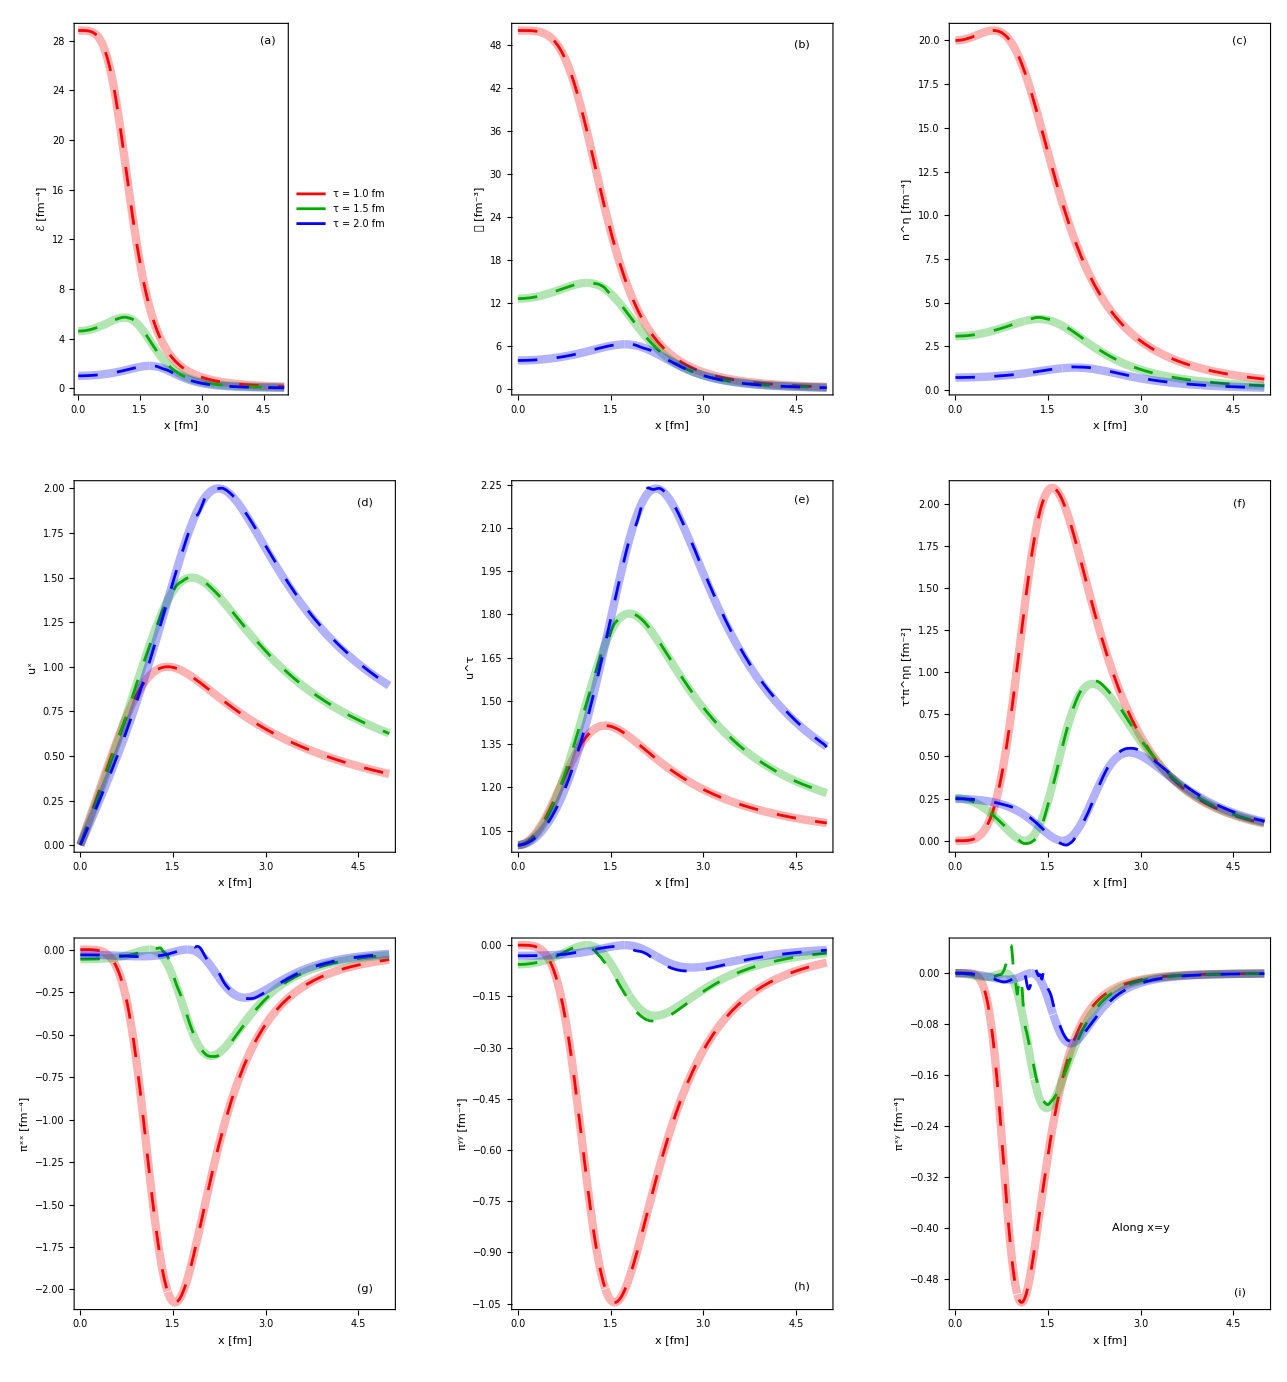

```mathematica
gubserISgrid=GraphicsGrid[{{edPlot,nPlot,nnPlot},{uxPlot,utPlot,pinnPlot},{pixxPlot,piyyPlot,pixyPlot}},Spacings->{25, -10}]
```

```mathematica
Export["Gubser_test.pdf",gubserISgrid]
```

Gubser_test.pdf

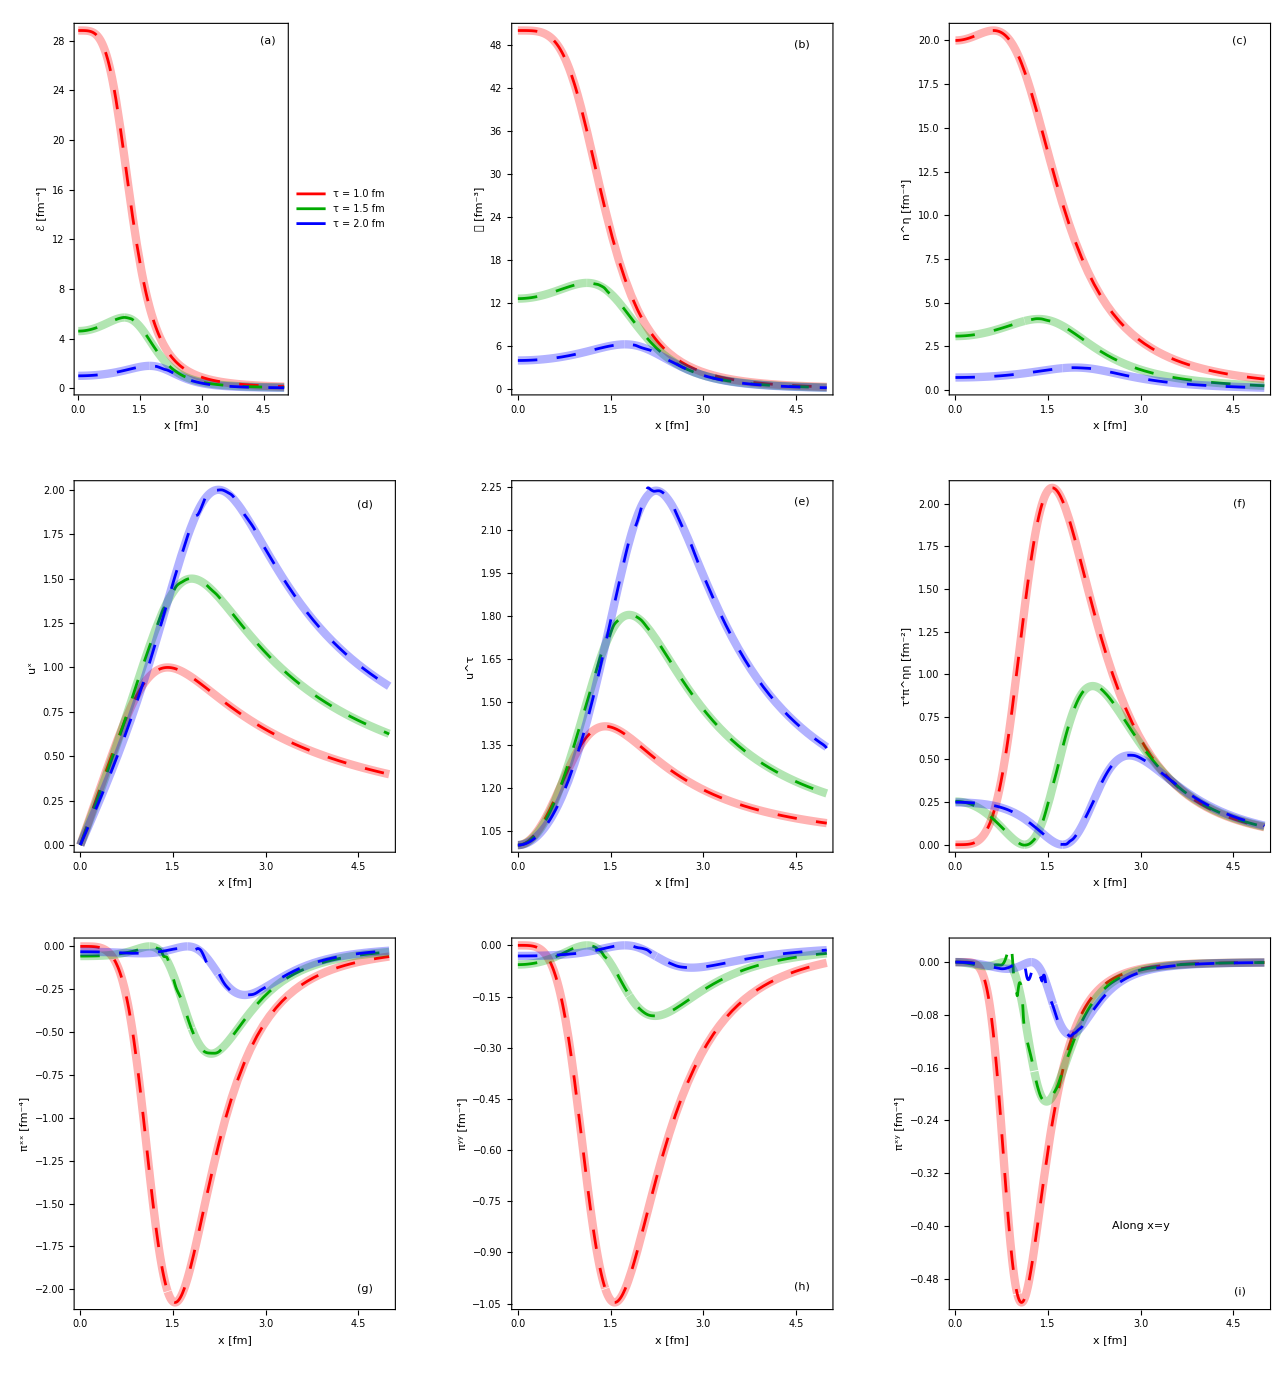

```mathematica
gubserISgrid=GraphicsGrid[{{edPlot,nPlot,nnPlot},{uxPlot,utPlot,pinnPlot},{pixxPlot,piyyPlot,pixyPlot}},Spacings->{25, -10}]
```

```mathematica
Export["Gubser_test_NonNewton.pdf",gubserISgrid]
```

Gubser_test_NonNewton.pdf